# Question 2:

Morse potential v.s. harmonic oscillator potential

```mathematica
ClearAll["Global`*"]
(*Defining helping function*)
MorseV[x_]:=d (1-Exp[-β x])^2
HarmV[x_]:=1/2 k x^2
```

## A. Taylor expansion of Morse func

```mathematica
Series[MorseV[x], {x, x0, 10}]  /.x0->0
```

d β^2 x^2-d β^3 x^3+7/12 d β^4 x^4-1/4 (d β^5) x^5+31/360 d β^6 x^6-1/40 (d β^7) x^7+(127 d β^8 x^8)/20160-(17 (d β^9) x^9)/12096+(73 d β^10 x^10)/259200+O[x]^11

While we have even and odd power to the x term in the expansion. It’s neither an even nor an odd function.

## B. Plotting potential curves

```mathematica
(*Temporary set values in order to make plot*)
d:= 1; β:= 1; k:= 2;
```

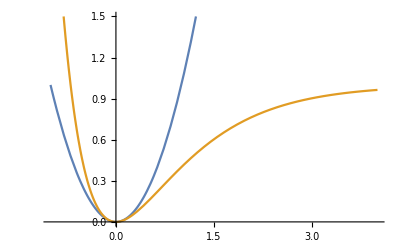

```mathematica
Plot[{HarmV[x], MorseV[x]}, {x, -1, 4}, PlotRange -> {0, 1.5}]
```

## C. Plotting potential curve difference

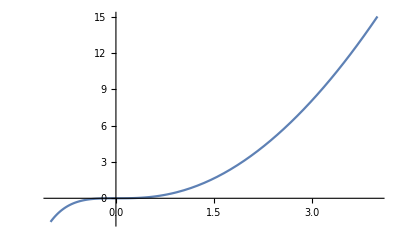

```mathematica
Plot[HarmV[x]-MorseV[x], {x, -1, 4}]
```

```mathematica
(*Cleaning up temporary parameters*)
Clear[d, β, k]
```

## D. Solve β for HCl

Prelude

```mathematica
(*Predefined constants*)
c := Quantity["SpeedOfLight"];
avo := Quantity["AvogadroConstant"];

(*SI Unit known parameters for HCl*)
ω:=Quantity[2866, 1/"Centimeters"];
μ:=Quantity[(35×1)/(35+1), ("Grams")/("Moles")] avo^-1
k:=(2π ω c)^2 μ
d:=Quantity[440.2,("Kilojoules")/("Moles")] avo^-1
```

Solving corresponding beta, and set it in situ.

```mathematica
Set @@@ Solve[{d β^2  ==  1/2 k, β>0} , β] [[1]];
```

Check the answer

```mathematica
Print[β]
```

1.79399×10^10 per meter

## E. Calculating energy based on the quantum number

```mathematica
(*Predefine constants*)
ℏ:=Quantity["ReducedPlanckConstant"];

(* Defining energy function based on 
* Harmonic / Morse Oscillator model
 *)
HarmEng[b_]:=(b+1/2) ℏ c ω 
MorseEng[b_]:=(b+1/2) ℏ c ω - (b+1/2)^2 (ℏ c ω)^2/(4d)
```

Caching energy difference results

```mathematica
quantNums := Range[1, 100];

engErrRate=(HarmEng[quantNums]-MorseEng[quantNums])/MorseEng[quantNums];
```

Getting result of the first state where energy difference larger than (...) error rates

```mathematica
First[ Position[engErrRate, _?(#>0.01&)] ]
```

{3}

```mathematica
First[ Position[engErrRate, _?(#>0.05&)] ]
```

{15}

Plotting energy difference ratio v.s. quantum numbers

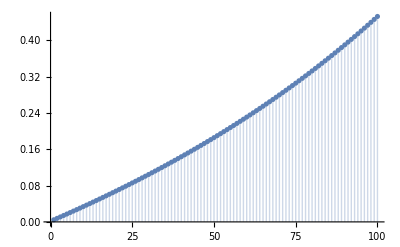

```mathematica
ListPlot[engErrRate, Filling->Axis]
```